Inversion W[x0]

```mathematica
Clear[λ0,τ,τR,β,δλ,x,W,x0,y]

ΔF = δλ/(2β λ0)-δλ^2/(4β λ0^2);


ΔF = x^2/2 δλ-(β(x^4/4-x^2/(4β λ0)))δλ^2/2;

g[y_]=y/τ;

W[x_]=Expand[ΔF+δλ^2/2 Assuming[τ>0, Integrate[(β(x^4/4-x^2/(4β λ0)))Exp[(-Abs[u-v])/τR]D[g[u],u]D[g[v],v],{u,0,τ},{v,0,τ}]]];

solve1=Solve[W[z]==y,z];

x0[y_,τ_]=z/.solve1[[4]];

f0[w_,t_]=Abs[D[x0[w,t],w]];
```

LRT PDF

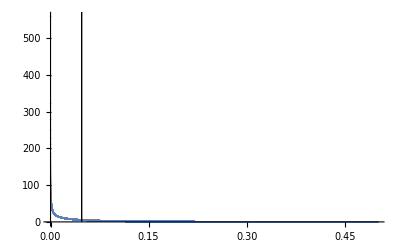

```mathematica
Clear[λ0,τR,τ,δλ,β,x,w]

λ0=1;
δλ=0.1;
τR=1;
τ=10;
β=1;

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

ρ0[x_]=Exp[-β/2 λ0 x^2]/(2π/ (β λ0))^(1/2);

Abs[2f0[w,τ]]ρ0[x0[w,τ]];

listaw=Table[{w,Abs[2f0[w,τ]]ρ0[x0[w,τ]]},{w,0.00001,0.5,0.00001}];

ListPlot[listaw,Epilog->{Line[{{ΔF,0},{ΔF,600}}]},PlotRange->{{0,0.5},Full}]

Clear[λ0,γ,τR,τ,δλ,β]
```

Initial parameters and important functions

```mathematica
Clear[λ0,γ,τR,τ,δλ,β,x0]

β=1;
γ=2;
λ0=1;
δλ=0.1;
τR = γ/(2λ0);
τ=10;

Nprocess=1000;

ρ0[y_]=Exp[-β/2 λ0 y^2]/(2π/ (β λ0))^(1/2);

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

dataWN=List[];
dataWLR=List[];
dataExpWN=List[];
dataExpWLR=List[];
(*dataCompLR=List[];
dataCompLR2=List[];*)

W[x0_]=Abs[1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])]

(*W[x0_]=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])*)
```

0.25 Abs[0.192406+1.53892×10^-22 (-1.31302×10^21+1.29961×10^21 x0^2)]

Numeric histogram

1.00235

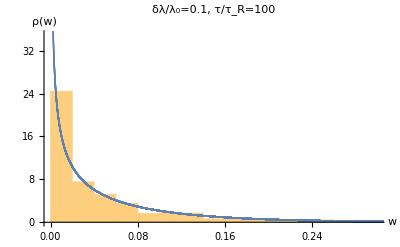

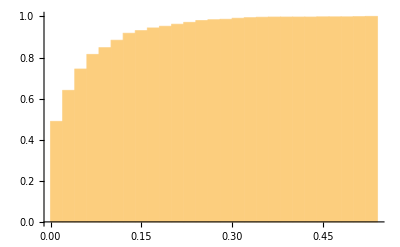

```mathematica
Do[

x0=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];

dataWN=AppendTo[dataWN,W[x0]];
dataExpWN=AppendTo[dataExpWN,Exp[-β(W[x0]-ΔF)]];

,{n,1,Nprocess}];

Mean[dataExpWN]

(*dataCompLR=AppendTo[dataCompLR,{Mean[dataWN]/(ΔF+β/2 Variance[dataWN]),δλ/λ0}]*)
(*FindDistribution[dataWN]

DistributionFitTest[dataWN,FindDistribution[dataWN]]*)

g1=Histogram[dataWN,Automatic,"PDF",PlotRange->{{0,0.3},{0,35}}];

g2=ListPlot[listaw,PlotRange->Full];

Show[{g1,g2},AxesLabel->{"w","ρ(w)"},PlotLabel->"δλ/λ_0=0.1, τ/τ_R=100"]

Histogram[dataWN,Automatic,"CDF",PlotRange->Full]
```

Error analysis

```mathematica
Do[

x0=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];

dataWN=AppendTo[dataWN,W[x0]];
dataExpWN=AppendTo[dataExpWN,Exp[-β(W[x0]-ΔF)]];

,{n,1,Nprocess}];

Mean[dataExpWN]

dataCompLR=AppendTo[dataCompLR,{Mean[dataWN]/(ΔF+β/2 Variance[dataWN]),δλ/λ0}]
```

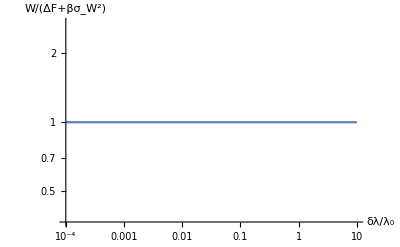

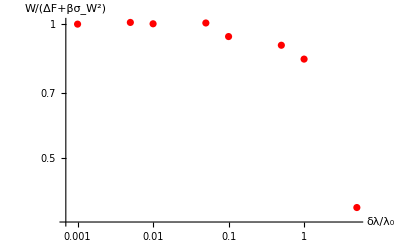

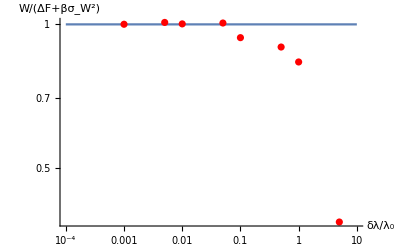

```mathematica
lista={{0.01,1.0023165868249073},{0.05,1.0065559374341098},{0.1,0.938061870974432},{0.5,0.8966495067015605},{1,0.8344073201603287},{0.005,1.0093776124294052},{0.001,1.0005616385358354},{5,0.3861146817272218}};

g1 = LogLogPlot[1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","W/(ΔF+βσ_W^2)"},PlotRange->Full];

g2=ListLogLogPlot[lista,AxesLabel->{"δλ/λ_0","W/(ΔF+βσ_W^2)"},PlotRange->Full,PlotStyle->{Red}];

Show[{g1,g2}]
```

Moment analysis

```mathematica
Clear[λ0,γ,τR,τ,δλ,β,x0]

β=1;
γ=2;
λ0=1;
δλ=5;
τR = γ/(2λ0);
τ=1;

Nprocess=10000;

ρ0[y_]=Exp[-β/2 λ0 y^2]/(2π/ (β λ0))^(1/2);

ΔF=N[-Log[(β λ0)^(1/2)/(β (δλ+λ0))^(1/2)]/β];

dataWN=List[];
dataWLR=List[];
dataExpWN=List[];
dataExpWLR=List[];
(*dataCompLR=List[];
dataCompLR2=List[];
dataCompLR3=List[];
dataCompLR4=List[];*)

(* Second-order approximation to avoid error for small δλ/λ0 *)

W[x0_]=Simplify[Abs[1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR](1+τ/(2τR)δλ/λ0)) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])]];

(* Exact work  *)

W[x0_]=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])
```

((Erf[3 √(2/5)]-Erf[1/(√10)]) (5 ⅇ^(1/10) √(2 π) x0^2-√5 π Erfi[1/(√10)])+(36 HypergeometricPFQ[{1,1},{3/2,2},-18/5])/(√5)-HypergeometricPFQ[{1,1},{3/2,2},-1/10]/(√5))/(4 √5)

```mathematica
Do[

x0=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];

dataWN=AppendTo[dataWN,W[x0]];
dataWLR=AppendTo[dataWLR,(x0^2 δλ)/2-1/8 x0^4 β δλ^2+(x0^2 δλ^2)/(8 λ0)+(x0^4 β δλ^2 τR)/(4 τ)-(x0^2 δλ^2 τR)/(4 λ0 τ)-(x0^4 β δλ^2 τR^2)/(4 τ^2)+(ⅇ^(-τ/τR) x0^4 β δλ^2 τR^2)/(4 τ^2)+(x0^2 δλ^2 τR^2)/(4 λ0 τ^2)-(ⅇ^(-τ/τR) x0^2 δλ^2 τR^2)/(4 λ0 τ^2)];

dataExpWN=AppendTo[dataExpWN,Exp[-β(W[x0]-ΔF)]];

,{n,1,Nprocess}];

Mean[dataExpWN]

dataCompLR=AppendTo[dataCompLR,{δλ/λ0,Abs[(Mean[dataWN]-Mean[dataWLR])/Mean[dataWN]]}]

dataCompLR2=AppendTo[dataCompLR2,{δλ/λ0,Abs[(Variance[dataWN]-Variance[dataWLR])/Variance[dataWN]]}]

dataCompLR3=AppendTo[dataCompLR3,{δλ/λ0,Abs[(Skewness[dataWN]-Skewness[dataWLR])/Skewness[dataWN]]}]

dataCompLR4=AppendTo[dataCompLR4,{δλ/λ0,Abs[(Kurtosis[dataWN]-Kurtosis[dataWLR])/Kurtosis[dataWN]]}]
```

0.821316

{{0.005,0.00152705},{0.001,0.000334252},{0.01,0.0027483},{0.05,0.0109345},{0.1,0.0207082},{0.5,0.143026},{1,0.346523},{5,0.898025},{5,0.401758}}

{{0.005,0.0078509},{0.001,0.00160127},{0.01,0.0152828},{0.05,0.0675679},{0.1,0.118178},{0.5,0.484629},{1,0.752135},{5,0.839233},{5,6.57664}}

{{0.005,0.00309024},{0.001,0.000545337},{0.01,0.00716896},{0.05,0.0382553},{0.1,0.114745},{0.5,0.375881},{1,0.616613},{5,5.77382},{5,5.68757}}

{{0.005,0.00589852},{0.001,0.00101292},{0.01,0.0149188},{0.05,0.0634418},{0.1,0.212243},{0.5,0.585962},{1,0.710947},{5,16.2106},{5,18.7109}}

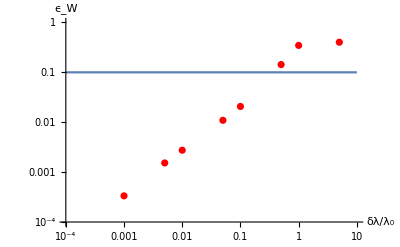

```mathematica
listaMean={{0.005,0.00152705321750806},{0.001,0.00033425203627367314},{0.01,0.0027482961018510665},{0.05,0.010934515714989046},{0.1,0.020708162143898794},{0.5,0.14302590850647978},{1,0.3465234508078323},{5,0.4017576538909527}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_W"},PlotRange->{{0.0001,10},{0.0001,1}}];

g2=ListLogLogPlot[listaMean,AxesLabel->{"δλ/λ_0","ϵ_W"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

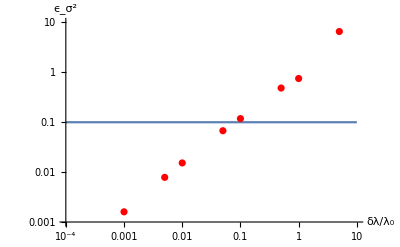

```mathematica
listaVar={{0.005,0.00785090397960738},{0.001,0.001601268753519751},{0.01,0.015282804973050498},{0.05,0.0675679296978002},{0.1,0.11817834658495521},{0.5,0.4846291450305237},{1,0.752134515108987},{5,6.576638729908318}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_(σ^2)"},PlotRange->{{0.0001,10},{0.001,10}}];

g2=ListLogLogPlot[listaVar,AxesLabel->{"δλ/λ_0","ϵ_(σ^2)"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

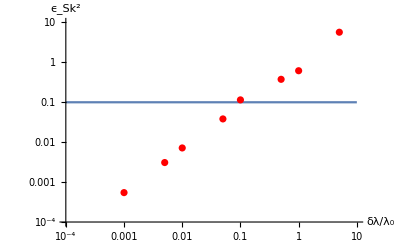

```mathematica
listaSkew={{0.005,0.003090237920211446},{0.001,0.0005453371534949376},{0.01,0.007168956071887804},{0.05,0.03825531752887722},{0.1,0.11474492912220509},{0.5,0.3758807992846916},{1,0.61661303612679},{5,5.68757220385147}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_(Sk^2)"},PlotRange->{{0.0001,10},{0.0001,10}}];

g2=ListLogLogPlot[listaSkew,AxesLabel->{"δλ/λ_0","ϵ_(Sk^2)"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

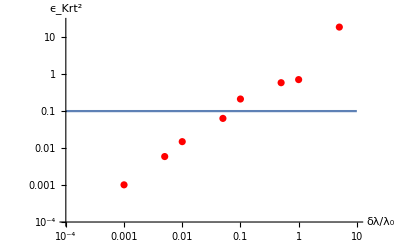

```mathematica
listaKurt={{0.005,0.00589851954299223},{0.001,0.0010129211128996206},{0.01,0.014918808665518023},{0.05,0.06344176044104005},{0.1,0.2122429715018512},{0.5,0.5859622927976306},{1,0.7109466063161474},{5,18.710906837765656}};

g1 = LogLogPlot[0.1,{x,0.0001,10},AxesLabel->{"δλ/λ_0","ϵ_(Krt^2)"},PlotRange->{{0.0001,10},{0.0001,25}}];

g2=ListLogLogPlot[listaKurt,AxesLabel->{"δλ/λ_0","ϵ_(Krt^2)"},PlotRange->{{0.0001,10},{0.001,1}},PlotStyle->{Red}];

Show[{g1,g2}]
```

Linear response histogram

0.926225

1.0092

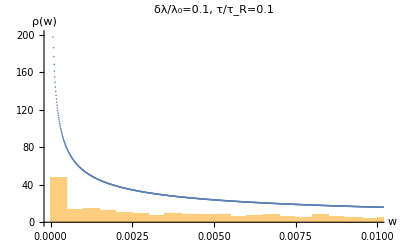

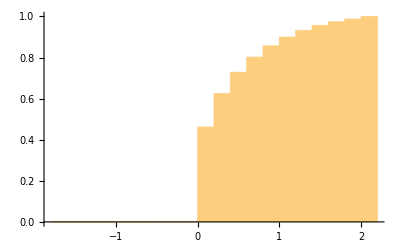

```mathematica
Do[

x=RandomVariate[ProbabilityDistribution[ρ0[y],{y,-Infinity,Infinity}]];
W=(x^2 δλ)/2-1/8 x^4 β δλ^2+(x^2 δλ^2)/(8 λ0)+(x^4 β δλ^2 τR)/(4 τ)-(x^2 δλ^2 τR)/(4 λ0 τ)-(x^4 β δλ^2 τR^2)/(4 τ^2)+(ⅇ^(-τ/τR) x^4 β δλ^2 τR^2)/(4 τ^2)+(x^2 δλ^2 τR^2)/(4 λ0 τ^2)-(ⅇ^(-τ/τR) x^2 δλ^2 τR^2)/(4 λ0 τ^2);

dataWLR=AppendTo[dataWLR,W];
dataExpWLR=AppendTo[dataExpWLR,Exp[-β(W-ΔF)]];

,{k,1,Nprocess}];

Mean[dataWLR]/(ΔF+β/2 Variance[dataWLR])

Mean[dataExpWLR]

g1=Histogram[dataWLR,{0.0005},"PDF",PlotRange->{{0,0.01},{0,200}}];

g2=ListPlot[listaw];

Show[{g1,g2},AxesLabel->{"w","ρ(w)"},PlotLabel->"δλ/λ_0=0.1, τ/τ_R=0.1"]

Histogram[dataWLR,Automatic,"CDF",PlotRange->Full]
```

Calculation of exact W

```mathematica
Clear[λ0,δλ,τ,β,γ,τR]
DSolve[{D[y[t],t]+(λ0+t δλ/τ)/(τR λ0)y[t]-1/(β τR λ0)==0,y[0]==y0},y[t],t]
```

{{y[t]→(ⅇ^(-t/τR-(t^2 δλ)/(2 λ0 τ τR)-(λ0 τ)/(2 δλ τR)) (2 ⅇ^((λ0 τ)/(2 δλ τR)) y0 β √δλ √λ0 √τR-√(2 π) √τ Erfi[(√λ0 √τ)/(√2 √δλ √τR)]+√(2 π) √τ Erfi[(t δλ+λ0 τ)/(√2 √δλ √λ0 √τ √τR)]))/(2 β √δλ √λ0 √τR)}}

```mathematica
Assuming[{δλ>0,λ0>0,τR>0,τ>0,β>0},Integrate[δλ/(4 β √δλ √λ0 √τR τ)ⅇ^(-t/τR-(t^2 δλ)/(2 λ0 τ τR)-(λ0 τ)/(2 δλ τR)) (2 ⅇ^((λ0 τ)/(2 δλ τR)) y0 β √δλ √λ0 √τR-√(2 π) √τ Erfi[(√λ0 √τ)/(√2 √δλ √τR)]+√(2 π) √τ Erfi[(t δλ+λ0 τ)/(√2 √δλ √λ0 √τ √τR)]),{t,0,τ}]]
```

1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) y0 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)])

```mathematica
W=1/(4 β √(δλ λ0^3 τ τR^3))((-Erf[(√((λ0 τ)/(δλ τR)))/(√2)]+Erf[(δλ+λ0)/(√2 √((δλ λ0 τR)/τ))]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)]);

W=1/(4 β √(δλ λ0^3 τ τR^3))((√(2/π δλ/λ0 τ/τR)Exp[-λ0/(2 δλ)τ/τR]) (ⅇ^((λ0 τ)/(2 δλ τR)) √(2 π) x0^2 β δλ λ0^2 τR^2-π √(δλ λ0^3 τ τR^3) Erfi[(√((λ0 τ)/(δλ τR)))/(√2)])-√((λ0^5 τ^3 τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-(λ0 τ)/(2 δλ τR)]+(δλ+λ0)^2 τ √((λ0 τ τR)/δλ) HypergeometricPFQ[{1,1},{3/2,2},-((δλ+λ0)^2 τ)/(2 δλ λ0 τR)]);
```

```mathematica
W[x0_]=(x0^2 δλ)/2-1/8 x0^4 β δλ^2+(x0^2 δλ^2)/(8 λ0)+(x0^4 β δλ^2 τR)/(4 τ)-(x0^2 δλ^2 τR)/(4 λ0 τ)-(x0^4 β δλ^2 τR^2)/(4 τ^2)+(ⅇ^(-τ/τR) x0^4 β δλ^2 τR^2)/(4 τ^2)+(x0^2 δλ^2 τR^2)/(4 λ0 τ^2)-(ⅇ^(-τ/τR) x0^2 δλ^2 τR^2)/(4 λ0 τ^2);
solve=Solve[D[W[x],x]==0,x];
y=x/.solve[[3]];
f[x_]=D[W[x],{x,2}];
Series[FullSimplify[W[y]],{δλ,0,2}]
```

(ⅇ^(τ/τR) τ^2)/(2 β (-2 τR^2+ⅇ^(τ/τR) (τ^2-2 τ τR+2 τR^2)))+δλ/(4 β λ0)+(ⅇ^(-τ/τR) (-2 τR^2+ⅇ^(τ/τR) (τ^2-2 τ τR+2 τR^2)) δλ^2)/(32 β λ0^2 τ^2)+O[δλ]^3